```mathematica
n = 3
f = Piecewise[{{1,1<x<3-1/n},{3*n*(x-3+1/n)+1,3-1/n<x<3}}]
```

3

Piecewise[{{1, 1<x<8/3}, {1+9 (-8/3+x), 8/3<x<3}, {0, True}}]

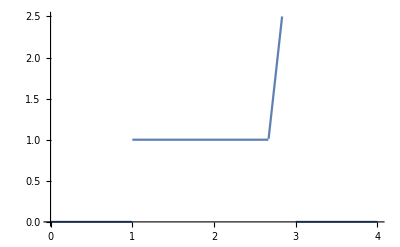

```mathematica
Plot[f, {x, 0, 4}]
```

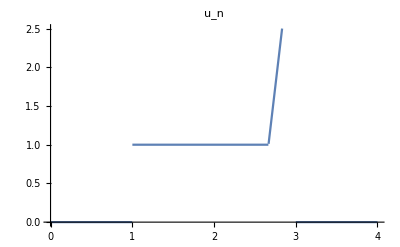

```mathematica
Plot[f,{x,0,4}, PlotLabel->"u_n"]
```

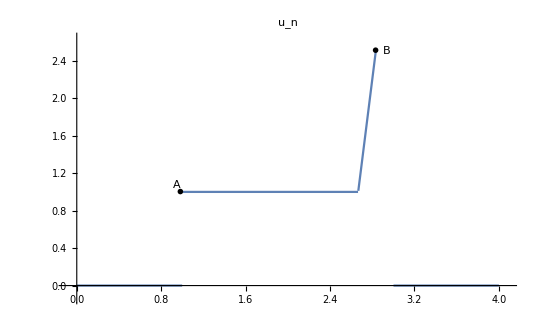

```mathematica
Plot[{-UnitBox[x-1],UnitBox[x-3]},{x,0, 4}, PlotLabels->Placed["v(x)", 1.4]]
```

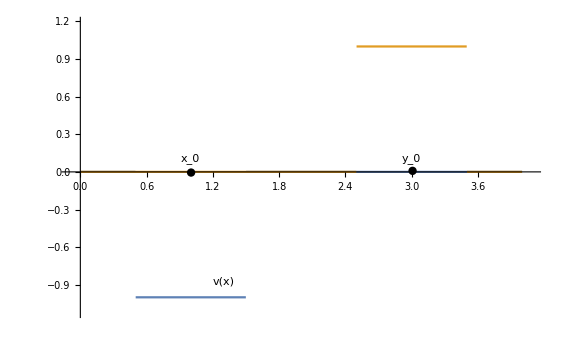

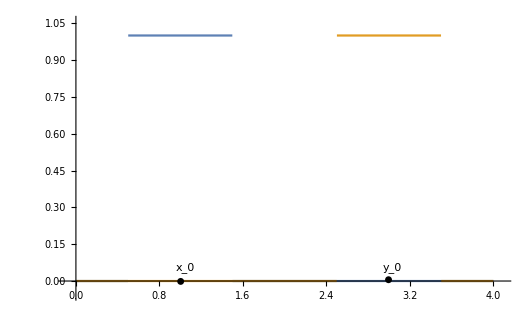

```mathematica
Plot[(x^2-1)^2,{x,-1.5,1.5}, PlotLabels->(p^2 - 1)^2 , PlotLabel->"Doppio pozzo"]
```

-Graphics-